```mathematica
(*************************************************)
(*************************************************)
(* The authors of this code are                      *)
(* Kim V. Berghaus and Yutaro Shoji                  *)
(* Please cite 2112.09702 if you use this notebook   *)
(* December 17th, 2021                               *) 
(* kim.berghaus@stonybrook.edu                       *)
(* yutaro.shoji@mail.huji.ac.il                      *)
(*************************************************)
(*************************************************)
```

# Phonon Background

```mathematica
path= NotebookDirectory[];
```

## Constants

```mathematica
keVTokg=1.783*^-33*kg;
icmtokeV=1.973*^-8;
vincmps=2.998*^10 cm/s;
spyear=60*60*24*365(s/year);
ikeVtocm=1.973*^-8 (cm/keV);
α=0.007297;
me=511.0;(*electron mass in keV*)
MNGe=6.765*^7;
MNSi=2.616*^7;
MNC=1.119*^7;
MNGa=6.495*^7;
MNAs=6.979*^7;
MNAl=2.513*^7;
MNO=1.490*^7;
NTSi=1/(MNSi*keVTokg);(*number of silicion particles/kg*)
NTGe=1/(MNGe*keVTokg);
NTGaAs=1/((MNGa +MNAs)keVTokg);(*number of GaAs molecules/kg*)
NTGaAsGa=NTGaAs;
NTGaAsAs=NTGaAs;
NTSiC=1/((MNSi+MNC)*keVTokg);
NTSiCSi=NTSiC;
NTSiCC=NTSiC;
NTAl2O3=1/((3*MNO+2*MNAl)keVTokg);(*number of Al3O2 molecules/kg, molar mass = 101.96 g/mol*)
NTAl2O3Al=2NTAl2O3 ;
NTAl2O3O=3NTAl2O3;
```

## Signal GaAs

### from https://arxiv.org/pdf/1910.08092.pdf

```mathematica
hm10={308.2827216089995,1737.5392525289546,2419.695977157717,6971.791769248949,13580.619242210725,7729.9720572130955,1900.6562193793038,635.7649050566099,885.1044848903508,1133.567970047748,1974.5665825479743,2198.6900734407386,1087.7607587013995,1741.904001102644,3688.9981905304817,7187.000940814769,682.8383169040131,10^-8};
hm1={31.126189325639643,54.214833035155294,60.33732187405113,243.15688748201035,338.6201155467752,277.2258951407639,144.91391923877822,144.3589342009516,206.82730591717967,206.82730591717967,358.49652806898854,356.9654945419164,197.56353703766004,454.8833890156425,728.7577532231315,1166.8362795200073,28.967588417689246,10^-8};
hm01={456.02606917122046,1737.7956994253996,988.773537372452,111.13982217781748,0.21049172187989407,0,0,0,0,0,0,0,0,0,0,0.4509065095484821,10^-8};
lm10={26271.902604675663,13400.427210994556,4671.878346444268,2924.837181035148,2601.682149967308,1628.7874214985482,855.4672535565667,619.973150025558,476.39380104013213,423.7587160604046,449.3061600600449,388.1352179939232,176.10136077199263,355.5064279213931,657.3499135734733,1180.412767677829,61.395366074226786,10^-8};
lm1={2601.6821499673106,1288.752413238365,423.7587160604055,209.910372010855,123.94252485211939,79.8991893238432,59.624359780327524,40.75392965871761,29.535136548350142,21.40466694217516,16.447568163493084,7.6841037554689455,2.601682149967303,7.2471873990272115,7.6841037554689455,16.93610584916726,0.9070414181116753,10^-8};
lm01={1.0145991833857213,209.910372010855,65.0967523045815,4.671878346444268,0.12762395627383402,10^-8,0,0,0,0,0,0,0,0,0,0.005568813990945245,0};
tab1=Table[j,{j,0,36,2.0}];
Khm10[ω_]:=Piecewise[Table[{Max[hm10[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];;
Klm10[ω_]:=Piecewise[Table[{Max[lm10[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Khm1[ω_]:=Piecewise[Table[{Max[hm1[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Klm1[ω_]:=Piecewise[Table[{Max[lm1[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Khm01[ω_]:=Piecewise[Table[{Max[hm01[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Klm01[ω_]:=Piecewise[Table[{Max[lm01[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
```

### from DarkElf (https://arxiv.org/abs/2104.12786)

```mathematica
SetDirectory[FileNameJoin[{path,"DARKELF_GaAs"}]];
omegaeV=Import["omega.csv"]//Flatten;
gaas10MeV = Import["gaas10MeV.csv"]//Flatten;
gaas1MeV = Import["gaas1MeV.csv"]//Flatten;
gaas01MeV = Import["gaas01MeV.csv"]//Flatten;
gaas001MeV = Import["gaas001MeV.csv"]//Flatten;
(*For different materials or different masses use DARKELF directly to generate more signals https://github.com/tongylin/DarkELF*)
```

```mathematica
gaas10MeVint=Interpolation[Transpose[{omegaeV,gaas10MeV}]];
gaas1MeVint=Interpolation[Transpose[{omegaeV,gaas1MeV}]];
gaas01MeVint=Interpolation[Transpose[{omegaeV,gaas01MeV}]];
gaas001MeVint=Interpolation[Transpose[{omegaeV,gaas001MeV}]];
```

```mathematica
tab=Table[j,{j,0*10^-3,100.*10^-3,2.0*10^-3}];
DElm10[ω_]=Piecewise[Table[{Max[NIntegrate[gaas10MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm1[ω_]=Piecewise[Table[{Max[NIntegrate[gaas1MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm01[ω_]=Piecewise[Table[{Max[NIntegrate[gaas01MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm001[ω_]=Piecewise[Table[{Max[NIntegrate[gaas001MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
```

InterpolatingFunction::dmvali: The integration endpoint 0. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

## Loading phonon DOS

```mathematica
(*This section reads in the POS for monoatomic materials Si and Ge and the partial POS for GaAs, SiC, and Subscript[Al, 2] Subscript[O, 3] from various sources in the literature (add documentation). It standardizes the x-axis to be in keV and the overall normalization to be such that ∫ dω F(ω) = 1 for the POS and ∑_i ∫ dω Subscript[F, i](ω) = 1 for diatomic materials, where the sum is over each atom in the material*)
```

### Monoatomic Materials (Si, Ge)

```mathematica
SetDirectory[FileNameJoin[{path,"Phonon_DOS"}]];
Siphon=Sort[Import["Si_monoatomic.csv"]];
Siphonx=Siphon[[All,1]]*10^-3; (*convert eV input to keV*)
Siphony=Siphon[[All,2]]; 
Siphonyn=Siphony/NIntegrate[Interpolation[Transpose[{Siphonx,Siphony}],InterpolationOrder-> 1][x],{x,Siphonx[[1]],Siphonx[[-1]]}];(*normalize such that ∫ dω f(ω) = 1*)
SiDOS=Transpose[{Siphonx,Siphonyn}];
Gephon =Import["Ge_monoatomic.csv"];
Gephonx=Gephon[[All,1]]*10^-6; (*convert meV input to keV*)
Gephony=Gephon[[All,2]]; 
Gephonyn=Gephony/NIntegrate[Interpolation[Transpose[{Gephonx,Gephony}],InterpolationOrder-> 1][x],{x,0,Gephonx[[-1]]}];(*normalize such that ∫ dω f(ω) = 1*)
GeDOS=Transpose[{Gephonx,Gephonyn}];
```

### Diatomic Materials (GaAs, SiC, Al_2 O_3)

#### GaAs

```mathematica
SetDirectory[FileNameJoin[{path,"Phonon_DOS"}]];
GaAsGa=Sort[Import["GaAs_Ga.csv"]];
GaAsAs=Sort[Import["GaAs_As.csv"]];
GaAsGax=GaAsGa[[All,1]]*(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
GaAsGay=GaAsGa[[All,2]];
GaAsAsx=GaAsAs[[All,1]]*(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
GaAsAsy=GaAsAs[[All,2]];
GaAsGayn =GaAsGay/(NIntegrate[Interpolation[Transpose[{GaAsGax,GaAsGay}],InterpolationOrder-> 1][x],{x,GaAsGax[[1]],GaAsGax[[-1]]}]+NIntegrate[Interpolation[Transpose[{GaAsAsx,GaAsAsy}],InterpolationOrder-> 1][x],{x,GaAsAsx[[1]],GaAsAsx[[-1]]}] );(*normalize such that ∫ dω Subscript[f, 1](ω) +Subscript[f, 2](ω) = 1*)
GaAsAsyn =GaAsAsy/(NIntegrate[Interpolation[Transpose[{GaAsGax,GaAsGay}],InterpolationOrder-> 1][x],{x,GaAsGax[[1]],GaAsGax[[-1]]}]+NIntegrate[Interpolation[Transpose[{GaAsAsx,GaAsAsy}],InterpolationOrder-> 1][x],{x,GaAsAsx[[1]],GaAsAsx[[-1]]}] );
GaAsGapDOS=Transpose[{GaAsGax,GaAsGayn}];
GaAsAspDOS=Transpose[{GaAsAsx,GaAsAsyn}];
```

#### SiC

```mathematica
SiCSi=Sort[Import["SiC_Si.csv"]];
SiCC=Sort[Import["SiC_C.csv"]];
SiCSix =  SiCSi[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
SiCSiy = SiCSi[[All,2]];
SiCCx =  SiCC[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
SiCCy = SiCC[[All,2]];
SiCSiyn = SiCSiy/(NIntegrate[Interpolation[Union[Transpose[{SiCSix,SiCSiy}],SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1][x],{x,SiCSix[[1]],SiCSix[[-1]]}]+NIntegrate[Interpolation[Transpose[{SiCCx,SiCCy}],InterpolationOrder-> 1][x],{x,SiCCx[[1]],SiCCx[[-1]]}] );(*normalize such that ∫ dω Subscript[f, 1](ω) +Subscript[f, 2](ω) = 1*)
SiCCyn = SiCCy/(NIntegrate[Interpolation[Union[Transpose[{SiCSix,SiCSiy}],SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1][x],{x,SiCSix[[1]],SiCSix[[-1]]}]+NIntegrate[Interpolation[Transpose[{SiCCx,SiCCy}],InterpolationOrder-> 1][x],{x,SiCCx[[1]],SiCCx[[-1]]}] );
SiCSipDOS=Transpose[{SiCSix,SiCSiyn}];
SiCSipDOS=Union[SiCSipDOS,SameTest->(#1[[1]]==#2[[1]]&)];
SiCCpDOS=Transpose[{SiCCx,SiCCyn}];
```

#### Al_2 O_3

```mathematica
Al2O3Al=Sort[Import["Al2O3_Al.csv"]];
Al2O3O=Sort[Import["Al2O3_O.csv"]];
Al2O3Alx =  Al2O3Al[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
Al2O3Aly = Al2O3Al[[All,2]];
Al2O3Ox =  Al2O3O[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
Al2O3Oy = Al2O3O[[All,2]];
Al2O3Alyn = Al2O3Aly/(2*NIntegrate[Interpolation[Transpose[{Al2O3Alx,Al2O3Aly}],InterpolationOrder-> 1][x],{x,Al2O3Alx[[1]],Al2O3Alx[[-1]]}]+3*NIntegrate[Interpolation[Transpose[{Al2O3Ox,Al2O3Oy}],InterpolationOrder-> 1][x],{x,Al2O3Ox[[1]],Al2O3Ox[[-1]]}] );(*normalize such that ∫ dω 2 Subscript[F, Al](ω) +3 Subscript[F, O](ω) = 1*)
Al2O3Oyn = Al2O3Oy/(2*NIntegrate[Interpolation[Transpose[{Al2O3Alx,Al2O3Aly}],InterpolationOrder-> 1][x],{x,Al2O3Alx[[1]],Al2O3Alx[[-1]]}]+3*NIntegrate[Interpolation[Transpose[{Al2O3Ox,Al2O3Oy}],InterpolationOrder-> 1][x],{x,Al2O3Ox[[1]],Al2O3Ox[[-1]]}] );
Al2O3AlpDOS=Transpose[{Al2O3Alx,Al2O3Alyn}];
Al2O3OpDOS=Transpose[{Al2O3Ox,Al2O3Oyn}];
```

## Loading form factors

```mathematica
(*read in the modified form factor g(q) (q[keV]) which acounts for relativistic corrections. Use the commented out section if you want to use the atomic form factor without relativistic corrections instead*)
```

```mathematica
(*modified atomic form factor for ions*)

SetDirectory[FileNameJoin[{path,"Form_factors","modifiedformfactors","large_q"}]];
FqGel=Import["mff_Ge4+.csv"];
FqSil=Import["mff_Si4+.csv"];
FqGal=Import["mff_Ga3+.csv"];
FqAsl=Import["mff_As5+.csv"];
FqCl=Import["mff_C4+.csv"];
FqAll=Import["mff_Al3+.csv"];
FqOl= Import["mff_O6+.csv"];
SetDirectory[FileNameJoin[{path,"Form_factors","modifiedformfactors","small_q"}]];
FqGes=Import["mff_Ge4+.csv"];
FqSis=Import["mff_Si4+.csv"];
FqGas=Import["mff_Ga3+.csv"];
FqAss=Import["mff_As5+.csv"];
FqCs=Import["mff_C4+.csv"];
FqAls=Import["mff_Al3+.csv"];
FqOs= Import["mff_O6+.csv"];
FqGe=Join[FqGes,FqGel];
FqSi=Join[FqSis,FqSil];
FqSi=Union[FqSi,SameTest->(#1[[1]]==#2[[1]]&)];(*removes duplicates*)
FqGa=Join[FqGas,FqGal];
FqAs=Join[FqAss,FqAsl];
FqC=Join[FqCs,FqCl];
FqC=Union[FqC,SameTest->(#1[[1]]==#2[[1]]&)];
FqAl=Join[FqAls,FqAll];
FqO=Join[FqOs,FqOl];

(**Modified atomic form factors

SetDirectory[FileNameJoin[{path,"Form_factors","modifiedformfactors","large_q"}]];
FqGel=Import["mff_Ge.csv"];
FqSil=Import["mff_Si.csv"];
FqGal=Import["mff_Ga.csv"];
FqAsl=Import["mff_As.csv"];
FqCl=Import["mff_C.csv"];
FqAll=Import["mff_Al.csv"];
FqOl= Import["mff_O.csv"];
SetDirectory[FileNameJoin[{path,"Form_factors","modifiedformfactors","small_q"}]];
FqGes=Import["mff_Ge.csv"];
FqSis=Import["mff_Si.csv"];
FqGas=Import["mff_Ga.csv"];
FqAss=Import["mff_As.csv"];
FqCs=Import["mff_C.csv"];
FqAls=Import["mff_Al.csv"];
FqOs= Import["mff_O.csv"];
FqGe=Join[FqGes,FqGel];
FqSi=Join[FqSis,FqSil];
FqSi=Union[FqSi,SameTest->(#1[[1]]==#2[[1]]&)];(*removes duplicates*)
FqGa=Join[FqGas,FqGal];
FqAs=Join[FqAss,FqAsl];
FqC=Join[FqCs,FqCl];
FqC=Union[FqC,SameTest->(#1[[1]]==#2[[1]]&)];
FqAl=Join[FqAls,FqAll];
FqO=Join[FqOs,FqOl];*)
```

```mathematica
(*Atomic form factors

SetDirectory[StringJoin[path,"\\Form_factors\\atomicformfactors\\small_q"]];
FqGes=Import["formfactor_Ge4+.csv"];
FqSis=Import["formfactor_Si4+.csv"];
FqGas=Import["formfactor_Ga.csv"];
FqAss=Import["formfactor_As.csv"];
FqCs=Import["formfactor_C.csv"];
FqAls=Import["formfactor_Al.csv"];
FqOs=Import["formfactor_O.csv"];
SetDirectory[StringJoin[path,"\\Form_factors\\atomicformfactors\\large_q"]];
FqGel=Import["formfactor_Ge4+.csv"];
FqSil=Import["formfactor_Si4+.csv"];
FqGal=Import["formfactor_Ga.csv"];
FqAsl=Import["formfactor_As.csv"];
FqCl=Import["formfactor_C.csv"];
FqAll=Import["formfactor_Al.csv"];
FqOl= Import["formfactor_O.csv"];
FqGe=Join[FqGes,FqGel];
FqSi=Join[FqSis,FqSil];
FqGa=Join[FqGas,FqGal];
FqAs=Join[FqAss,FqAsl];
FqC=Join[FqCs,FqCl];
FqAl=Join[FqAls,FqAll];
FqO=Join[FqOs,FqOl];*)
```

## Differential rate calculation

```mathematica
(*read in the modified form factor g(q) (q[keV]) which acounts for relativistic corrections. Use the commented out section if you want to use the atomic form factor without relativistic corrections instead*)
```

```mathematica
dσdq[pγ_,FF_]:=Module[{pγin=pγ,FFin=FF,Fq},
Fq=Interpolation[Union[FFin,SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1];

(q/pγin^2)(α^2/(2 me^2))(1+(1- q^2/(2 pγin^2))^2)(Fq[q])^2 2π ](*returns dσ/dq(q) where cos(θ) is rewritten as (1-q^2/(2 pγ^2)), and dcosθ/dq = q/pγ^2  *)
```

```mathematica
(*returns S(q,ω) up to n = 6 multiphonon contributions*)
M6[M_,DOS_]:=Module[{Min=M,DOSin=DOS,ωmax,ωmin,pDOS,DW,T2,T3,T4,T5,T6},
ωmin=DOSin[[All,1]][[1]];
ωmax=DOSin[[All,1]][[-1]];
pDOS[ω_]:=Piecewise[{{Interpolation[DOSin,InterpolationOrder-> 1][ω],ωmin<=ω<ωmax}}];
DW[q_]:=(q^2/(4 Min))NIntegrate[pDOS[ω]/ω,{ω,ωmin,ωmax}];
T2=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))(pDOS[ωp]/ωp),{ωp,ωmin,2ωmax}]},{ω,ωmin,2ωmax,2(ωmax/100)}],InterpolationOrder-> 1];
T3=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))T2[ωp],{ωp,ωmin,3ωmax}]},{ω,ωmin,3ωmax,3(ωmax/100)}],InterpolationOrder-> 1];
T4=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))T3[ωp],{ωp,ωmin,4ωmax}]},{ω,ωmin,4ωmax,4(ωmax/100)}],InterpolationOrder-> 1];
T5=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))T4[ωp],{ωp,ωmin,5ωmax}]},{ω,ωmin,5ωmax,5(ωmax/100)}],InterpolationOrder-> 1];
T6=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))T5[ωp],{ωp,ωmin,5ωmax}]},{ω,ωmin,5ωmax,5(ωmax/100)}],InterpolationOrder-> 1];
{ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]+(1/Factorial[3])(q^2/(2Min))^3 T3[ω]+(1/Factorial[4])(q^2/(2Min))^4 T4[ω]+(1/Factorial[5])(q^2/(2Min))^5 T5[ω]+(1/Factorial[6])(q^2/(2Min))^6 T6[ω]),ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]+(1/Factorial[3])(q^2/(2Min))^3 T3[ω]+(1/Factorial[4])(q^2/(2Min))^4 T4[ω]+(1/Factorial[5])(q^2/(2Min))^5 T5[ω]),ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]+(1/Factorial[3])(q^2/(2Min))^3 T3[ω]+(1/Factorial[4])(q^2/(2Min))^4 T4[ω]),ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]+(1/Factorial[3])(q^2/(2Min))^3 T3[ω]),ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]),ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω))}]
(*returns S(q,ω) with only single phonon contributions*)
M1[M_,DOS_]:=Module[{Min=M,DOSin=DOS,ωmax,ωmin,pDOS,DW,T2,T3},
ωmin=DOSin[[All,1]][[1]];
ωmax=DOSin[[All,1]][[-1]];
pDOS[ω_]:=Piecewise[{{Interpolation[DOSin,InterpolationOrder-> 1][ω],ωmin<=ω<ωmax}}];
DW[q_]:=(q^2/(4 Min))NIntegrate[pDOS[ω]/ω,{ω,ωmin,ωmax}];
ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω))]
```

```mathematica
(*returns list of phonon Rates per 2 meV bin as function of ω [keV] for up to n = 6 multi-phonon. Takes about ~15 minutes to run. Change last entry in tab to change bin size. 
Takes ion mass [keV], number of ions per target, form factor as function of q [keV], photon energy and density in format {{Subscript[E, γ1][keV],Subscript[n, γ1][cm^-3]},{Subscript[E, γ2][keV],Subscript[n, γ2][cm^-3]}...} as arguments *)
Rate[MN_,NT_,DOS_,FF_,γlist_]:=Module[{MNin=MN,DOSin=DOS,γin=γlist,FFin=FF,S1,S2,S3,S4,S5,S6,Rin1,Rin2,Rin3,Rin4,Rin5,Rin6,tab,listn},
listn=M6[MNin,DOSin];
S6[q_,ω1_]=listn[[1]]/.ω-> ω1;
S5[q_,ω1_]=listn[[2]]/.ω-> ω1;
S4[q_,ω1_]=listn[[3]]/.ω-> ω1;
S3[q_,ω1_]=listn[[4]]/.ω-> ω1;
S2[q_,ω1_]=listn[[5]]/.ω-> ω1;
S1[q_,ω1_]=listn[[6]]/.ω-> ω1;
Rin6[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S6[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
Rin5[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S5[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
Rin4[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S4[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
Rin3[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S3[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
Rin2[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S2[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
Rin1[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S1[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
tab=Table[j,{j,0*10^-3,0.1*10^-3,0.002*10^-3}];
{Piecewise[Table[{Max[Rin6[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]],Piecewise[Table[{Max[Rin5[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]],Piecewise[Table[{Max[Rin4[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]],Piecewise[Table[{Max[Rin3[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]],Piecewise[Table[{Max[Rin2[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]],Piecewise[Table[{Max[Rin1[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]]}//Quiet];


(*returns single phonon Rate as function of ω [keV]. Executes within seconds so use this function rather than full multi-phonon one to familarize yourself with the code. Change last entry in tab to change bin size. 
Takes ion mass [keV], number of ions per target, form factor as function of q [keV], photon energy and density in format {{Subscript[E, γ1][keV],Subscript[n, γ1][cm^-3]},{Subscript[E, γ2][keV],Subscript[n, γ2][cm^-3]}...} as arguments *)
Rate1n[MN_,NT_,DOS_,FF_,γlist_]:=Module[{MNin=MN,DOSin=DOS,γin=γlist,FFin=FF,S,Rin,tab},
S[q_,ω1_]=M1[MNin,DOSin]/.ω-> ω1;
Rin[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
tab=Table[j,{j,0*10^-3,0.1*10^-3,0.002*10^-3}];
Piecewise[Table[{Max[Rin[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]]//Quiet]
```

## Plots in arXiv: 2112.09702 (this takes ~2h)

### Plot Style

```mathematica
$PlotTheme="Classic";

Clear[fticksR,PrettyExp,fticksRNoLabels,fticksRlinear,fticksRlinearnoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]];
(* Axis for y versus x: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(*Axis for linear ticks*)
fticksRlinear[min_,max_,AMAX_,SUB_]:=Flatten[Table[Prepend[Flatten[Table[{x+i*AMAX/SUB,"",{.008,0}},{i,1,SUB-1}],{1}],{x,x,{.02,0}}],{x,Floor[min],Ceiling[max],AMAX}],1];

fticksRlinearnoLabels[min_,max_,AMAX_,SUB_]:=Flatten[Table[Prepend[Flatten[Table[{x+i*AMAX/SUB,"",{.008,0}},{i,1,SUB-1}],{1}],{x,"",{.02,0}}],{x,Floor[min],Ceiling[max],AMAX}],1];
fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

### Fig 2.

```mathematica
(*photon densities specified in Table 1 in "paper" as derived from EDELWEISS shielding *)
γin={{143,1.765691804296801*^-19},{163,1.4282500126809865*^-19},{185,1.6794808328201712*^-18},{208,1.392948378947999*^-18},{238,1.6652199331831083*^-17},{269,1.439000390299994*^-18},{295,5.465384505091963*^-18},{336,6.311850436744921*^-18},{350,8.333274687641328*^-18},{460,2.769624910501537*^-18},{1173,1.185071590578618*^-17},{1332,3.66208698747358*^-18},{1461,6.854167092808294*^-18},{2614,5.57863180115972*^-18}};
```

```mathematica
(*This takes ~30 - 40 minutes to execute*)
{RGaAs6nin[ω_],RGaAs5nin[ω_],RGaAs4nin[ω_],RGaAs3nin[ω_],RGaAs2nin[ω_],RGaAs1nin[ω_]}=Rate[MNGa,NTGaAsGa,GaAsGapDOS,FqGa,γin]+Rate[MNAs,NTGaAsAs,GaAsAspDOS,FqAs,γin]//Quiet;
{RSi6nin[ω_],RSi5nin[ω_],RSi4nin[ω_],RSi3nin[ω_],RSi2nin[ω_],RSi1nin[ω_]}=Rate[MNSi,NTSi,SiDOS,FqSi,γin]//Quiet;
{RGe6nin[ω_],RGe5nin[ω_],RGe4nin[ω_],RGe3nin[ω_],RGe2nin[ω_],RGe1nin[ω_]}=Rate[MNGe,NTGe,GeDOS,FqGe,γin]//Quiet;
{RSiC6nin[ω_],RSiC5nin[ω_],RSiC4nin[ω_],RSiC3nin[ω_],RSiC2nin[ω_],RSiC1nin[ω_]}=Rate[MNSi,NTSiCSi,SiCSipDOS,FqSi,γin]+Rate[MNC,NTSiCC,SiCCpDOS,FqC,γin]//Quiet;
{RAl2O36nin[ω_],RAl2O35nin[ω_],RAl2O34nin[ω_],RAl2O33nin[ω_],RAl2O32nin[ω_],RAl2O31nin[ω_]}=Rate[MNAl,NTAl2O3Al,Al2O3AlpDOS,FqAl,γin]+Rate[MNO,NTAl2O3O,Al2O3OpDOS,FqO,γin]//Quiet;
```

```mathematica
t1=0.0075;
t2=0.005;
p1=LogPlot[{ RGaAs6nin[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t2],Thick, Thick, Thick, Thick},PlotLegends-> Placed[{Style["GaAs",FontSize-> 20,FontFamily->"Times"]},{0.6,0.945}]];
p2=LogPlot[{ 0,RSi6nin[10^-6 ω]},{ω,0,130},PlotRange->{{0,100},{0.5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thickness[t2], Thick, Thick, Thick},PlotLegends-> Placed[{None,Style["Si",FontSize-> 20,FontFamily->"Times"]},{0.56,0.845}]];
p3=LogPlot[{ 0,0,RGe6nin[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thickness[t2], Thick, Thick},PlotLegends-> Placed[{None,None,Style["Ge",FontSize-> 20,FontFamily->"Times"]},{Right,Top}]];
p4=LogPlot[{0,0,0,RSiC6nin[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thickness[t2], Thick},PlotLegends-> Placed[{None,None,None,Style["SiC",FontSize-> 20,FontFamily->"Times"]},{Right,Top}]];
p5=LogPlot[{ 0,0,0,0,RAl2O36nin[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, {Thickness[t2],Lighter[Orange]}},PlotLegends-> Placed[{None,None,None,None,Style["Al_2O_3",FontSize-> 20,FontFamily->"Times",SingleLetterItalics->False]},{Right,Top}]];
Show[p1,p2,p3,p4,p5]
```

### Fig 3.

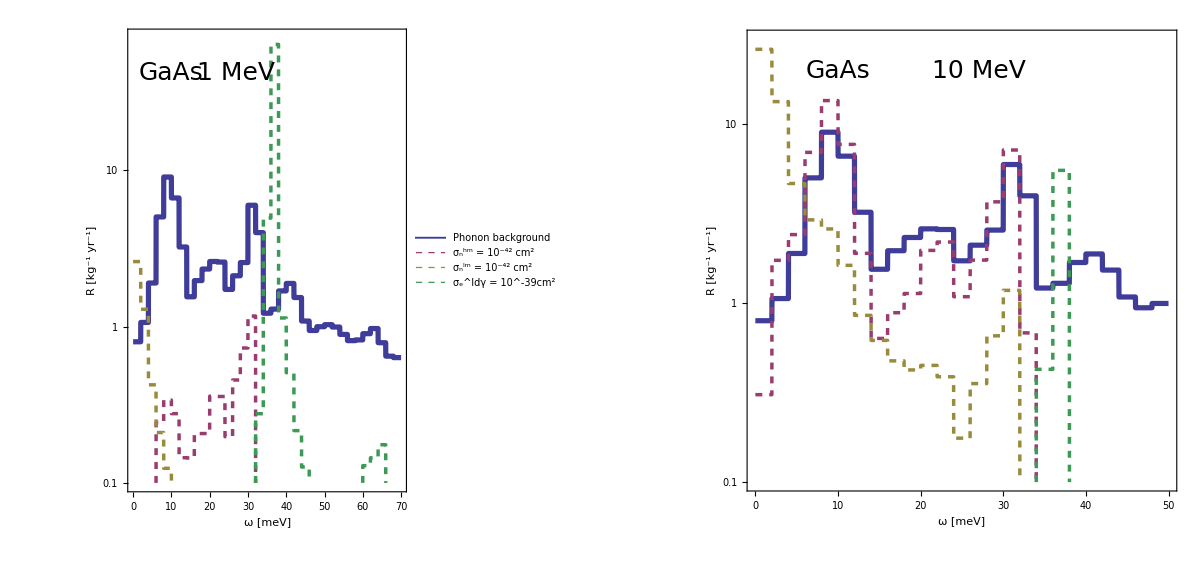

```mathematica
t1=0.0075;
t2=0.005;
style=Dashed;
myplot1=LogPlot[{RGaAs6nin[10^-6 ω], 10^-3 Khm10[ω],10^-3 Klm10[ω],10^-1 DElm10[10^-3 ω]},{ω,0,50},PlotRange->{{0,50},{0.1,30}},Frame->True,FrameTicks->{{fticksR[0.1,100,0],fticksRNoLabels[0.1,100,0]},{fticksRlinear[0,50,10,2],fticksRlinearnoLabels[0,50,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->FontSize-> 25,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize-> 70},PlotStyle-> {Thickness[t1],{ Thickness[t2],style},{Thickness[t2],style},{Thickness[t2],style},{Thickness[t2],style}},Epilog->{ Text[Style["10 MeV",FontSize-> 25,FontFamily->"Times"],{27,Log[20.0]}],Text[Style["GaAs",FontSize-> 25,FontFamily->"Times"],{10,Log[20.0]}]}];
myplot2=LogPlot[{ RGaAs6nin[10^-6 ω],10^-3 Khm1[ω],10^-3 Klm1[ω],10^-1 DElm1[10^-3 ω]},{ω,0,70},PlotRange->{{0,70},{0.1,70}},Frame->True,FrameTicks->{{fticksR[0.1,800,0],fticksRNoLabels[0.1,800,0]},{fticksRlinear[0,70,10,2],fticksRlinearnoLabels[0,70,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->25,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1], {Thickness[t2],style},{Thickness[t2],style},{Thickness[t2],style},{Thickness[t2],style}},PlotLegends->Placed[{Style["Phonon background",FontSize-> 18,FontFamily->"Times"], Style["σ_n^hm = 10^-43 cm^2",FontSize-> 18,FontFamily->"Times"],Style["σ_n^lm = 10^-43 cm^2",FontSize-> 18,FontFamily->"Times"], Style["σ_e^ldγ = 10^-39cm^2",FontSize-> 18,FontFamily->"Times"]},{{0.775,0.76}}],Epilog->{ Text[Style["1 MeV",FontSize-> 25,FontFamily->"Times"],{27,Log[42.0]}],Text[Style["GaAs",FontSize-> 25,FontFamily->"Times"],{10,Log[42.0]}]}];
GraphicsGrid[{{myplot2,myplot1}},ImageSize-> 1200]
```

### Fig. 4

```mathematica
γtest={{1461,4.694440000000001*^-16}};
```

```mathematica
{RGaAs6n[ω_],RGaAs5n[ω_],RGaAs4n[ω_],RGaAs3n[ω_],RGaAs2n[ω_],RGaAs1n[ω_]}=Rate[MNGa,NTGaAsGa,GaAsGapDOS,FqGa,γtest]+Rate[MNAs,NTGaAsAs,GaAsAspDOS,FqAs,γtest]//Quiet;
{RGe6n[ω_],RGe5n[ω_],RGe4n[ω_],RGe3n[ω_],RGe2n[ω_],RGe1n[ω_]}=Rate[MNGe,NTGe,GeDOS,FqGe,γtest]//Quiet;
{RSi6n[ω_],RSi5n[ω_],RSi4n[ω_],RSi3n[ω_],RSi2n[ω_],RSi1n[ω_]}=Rate[MNSi,NTSi,SiDOS,FqSi,γtest]//Quiet;
{RSiC6n[ω_],RSiC5n[ω_],RSiC4n[ω_],RSiC3n[ω_],RSiC2n[ω_],RSiC1n[ω_]}=Rate[MNSi,NTSiCSi,SiCSipDOS,FqSi,γtest]+Rate[MNC,NTSiCC,SiCCpDOS,FqC,γtest]//Quiet;
{RAl2O36n[ω_],RAl2O35n[ω_],RAl2O34n[ω_],RAl2O33n[ω_],RAl2O32n[ω_],RAl2O31n[ω_]}=Rate[MNAl,NTAl2O3Al,Al2O3AlpDOS,FqAl,γtest]+Rate[MNO,NTAl2O3O,Al2O3OpDOS,FqO,γtest]//Quiet;
```

#### GaAs

```mathematica
t1=0.005;
p6GaAs=LogPlot[{ RGaAs6n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],AbsoluteDashing[0.01]},PlotLegends->Placed[{Style["n ≤ 6",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.95}}],Epilog->{Text[Style["GaAs",FontSize-> 25,FontFamily->"Times"],{12,Log[6]}]}];
p5GaAs=LogPlot[{ RGaAs5n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],AbsoluteDashing[3]},PlotLegends->Placed[{Style["n ≤ 5",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.85}}]];
p4GaAs=LogPlot[{ RGaAs4n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],AbsoluteDashing[5]},PlotLegends->Placed[{Style["n ≤ 4",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.75}}]];
p3GaAs=LogPlot[{ RGaAs3n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],DotDashed},PlotLegends->Placed[{Style["n ≤ 3",FontSize-> 18,FontFamily->"Times"]},{{0.85,0.95}}]];
p2GaAs=LogPlot[{ RGaAs2n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],Dotted},PlotLegends->Placed[{Style["n ≤ 2",FontSize-> 18,FontFamily->"Times"]},{{0.85,0.85}}]];
p1GaAs=LogPlot[{ RGaAs1n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thickness[t1],AbsoluteDashing[7]},PlotLegends->Placed[{Style["n = 1",FontSize-> 18,FontFamily->"Times"]},{{0.85,0.75}}]];
t1p=Show[p6GaAs,p5GaAs,p4GaAs,p3GaAs,p2GaAs,p1GaAs]
```

#### Si

```mathematica
t1=0.005;
p6Si=LogPlot[{ 0,RSi6n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,0.8}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {{Black},{Thickness[t1],AbsoluteDashing[0.01]}},
PlotLegends->Placed[{None,Style["n ≤ 6",FontSize-> 18,FontFamily->"Times"]},{{0.15,0.3}}],
Epilog->{Text[Style["Si",FontSize-> 25,FontFamily->"Times"],{8,Log[0.5]}]}];
p5Si=LogPlot[{0,RSi5n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,Style["n ≤ 5",FontSize-> 18,FontFamily->"Times"]},{{0.15,0.2}}],
PlotStyle-> {{Black},{Thickness[t1],AbsoluteDashing[3]}}];
p4Si=LogPlot[{0,RSi4n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},
PlotLegends->Placed[{None,Style["n ≤ 4",FontSize-> 18,FontFamily->"Times"]},{{0.15,0.1}}],
PlotStyle-> {{Black},{Thickness[t1],AbsoluteDashing[5]}}];
p3Si=LogPlot[{0, RSi3n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,Style["n ≤ 3",FontSize-> 18,FontFamily->"Times"]},{{0.45,0.3}}],PlotStyle-> {{Black},{Thickness[t1],DotDashed}}];
p2Si=LogPlot[{0,RSi2n[10^-6 ω]},{ω,0,105},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,Style["n ≤ 2",FontSize-> 18,FontFamily->"Times"]},{{0.45,0.2}}],PlotStyle-> {{Black},{Thickness[t1],Dotted}}];
p1Si=LogPlot[{ 0,RSi1n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,140,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,Style["n = 1",FontSize-> 18,FontFamily->"Times"]},{{0.45,0.1}}],PlotStyle-> {{Black},{Thickness[t1],AbsoluteDashing[7]}}];
t2p=Show[p6Si,p5Si,p4Si,p3Si,p2Si,p1Si]
```

#### Ge

```mathematica
t1=0.005;
p6Ge=LogPlot[{0, 0,RGe6n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,4}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {{Black},{Black},{Thickness[t1],AbsoluteDashing[0.01]}},
PlotLegends->Placed[{None,None,Style["n ≤ 6",FontSize-> 18,FontFamily->"Times"]},{{0.2,0.3}}],
Epilog->{Text[Style["Ge",FontSize-> 25,FontFamily->"Times"],{25,Log[2]}]}];
p5Ge=LogPlot[{0,0,RGe5n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,Style["n ≤ 5",FontSize-> 18,FontFamily->"Times"]},{{0.2,0.2}}],
PlotStyle-> {{Black},{Black},{Thickness[t1],AbsoluteDashing[3]}}];
p4Ge=LogPlot[{0,0,RGe4n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},
PlotLegends->Placed[{None,None,Style["n ≤ 4",FontSize-> 18,FontFamily->"Times"]},{{0.2,0.1}}],
PlotStyle-> {{Black},{Black},{Thickness[t1],AbsoluteDashing[5]}}];
p3Ge=LogPlot[{0,0, RGe3n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,Style["n ≤ 3",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.3}}],PlotStyle-> {{Black},{Black},{Thickness[t1],DotDashed}}];
p2Ge=LogPlot[{0,0,RGe2n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,Style["n ≤ 2",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.2}}],PlotStyle-> {{Black},{Black},{Thickness[t1],Dotted}}];
p1Ge=LogPlot[{ 0,0,RGe1n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,140,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,Style["n = 1",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.1}}],PlotStyle-> {{Black},{Black},{Thickness[t1],AbsoluteDashing[7]}}];
t3p=Show[p6Ge,p5Ge,p4Ge,p3Ge,p2Ge,p1Ge]
```

#### SiC

```mathematica
t1=0.005;
p6SiC=LogPlot[{0, 0,0,RSiC6n[10^-6 ω]},{ω,0,155},PlotRange->{{0,100},{5*10^-3,0.25}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {{Black},{Black},{Black},{Thickness[t1],AbsoluteDashing[0.01]}},
PlotLegends->Placed[{None,None,None,Style["n ≤ 6",FontSize-> 18,FontFamily->"Times"]},{{0.27,0.3}}],
Epilog->{Text[Style["SiC",FontSize-> 25,FontFamily->"Times"],{10,Log[0.15]}]}];
p5SiC=LogPlot[{0,0,0,RSiC5n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,Style["n ≤ 5",FontSize-> 18,FontFamily->"Times"]},{{0.27,0.2}}],
PlotStyle-> {{Black},{Black},Black,{Thickness[t1],AbsoluteDashing[3]}}];
p4SiC=LogPlot[{0,0,0,RSiC4n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},
PlotLegends->Placed[{None,None,None,Style["n ≤ 4",FontSize-> 18,FontFamily->"Times"]},{{0.27,0.1}}],
PlotStyle-> {{Black},{Black},Black,{Thickness[t1],AbsoluteDashing[5]}}];
p3SiC=LogPlot[{0,0,0, RSiC3n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,Style["n ≤ 3",FontSize-> 18,FontFamily->"Times"]},{{0.57,0.3}}],PlotStyle-> {{Black},{Black},Black,{Thickness[t1],DotDashed}}];
p2SiC=LogPlot[{0,0,0,RSiC2n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,Style["n ≤ 2",FontSize-> 18,FontFamily->"Times"]},{{0.57,0.2}}],PlotStyle-> {{Black},{Black},Black,{Thickness[t1],Dotted}}];
p1SiC=LogPlot[{ 0,0,0,RSiC1n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,140,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,Style["n = 1",FontSize-> 18,FontFamily->"Times"]},{{0.57,0.1}}],PlotStyle-> {{Black},{Black},Black,{Thickness[t1],AbsoluteDashing[7]}}];
t4p=Show[p6SiC,p5SiC,p4SiC,p3SiC,p2SiC,p1SiC]
```

#### Al_2 0_3 (multi-phonon may not hold up this material due to missing cubic symmetry)

```mathematica
t1=0.005;
p6Al2O3=LogPlot[{0, 0,0,0,RAl2O36n[10^-6 ω]},{ω,0,155},PlotRange->{{0,100},{5*10^-3,0.1}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {{Black},{Black},{Black},Black,{Orange,Thickness[t1],AbsoluteDashing[0.01]}},
PlotLegends->Placed[{None,None,None,None,Style["n ≤ 6",FontSize-> 18,FontFamily->"Times"]},{{0.23,0.3}}],
Epilog->{Text[Style["Al_2O_3",FontSize-> 25,SingleLetterItalics->False,FontFamily->"Times"],{10,Log[0.08]}]}];
p5Al2O3=LogPlot[{0,0,0,0,RAl2O35n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,None,Style["n ≤ 5",FontSize-> 18,FontFamily->"Times"]},{{0.23,0.2}}],
PlotStyle-> {{Black},{Black},Black,Black,{Orange,Thickness[t1],AbsoluteDashing[3]}}];
p4Al2O3=LogPlot[{0,0,0,0,RAl2O34n[10^-6 ω]},{ω,0,150},PlotRange->{{0,100},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},
PlotLegends->Placed[{None,None,None,None,Style["n ≤ 4",FontSize-> 18,FontFamily->"Times"]},{{0.23,0.1}}],
PlotStyle-> {{Black},{Black},Black,Black,{Orange,Thickness[t1],AbsoluteDashing[5]}}];
p3Al2O3=LogPlot[{0,0,0,0, RAl2O33n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,None,Style["n ≤ 3",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.3}}],PlotStyle-> {{Black},{Black},Black,Black,{Orange,Thickness[t1],DotDashed}}];
p2Al2O3=LogPlot[{0,0,0,0,RAl2O32n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,None,Style["n ≤ 2",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.2}}],PlotStyle-> {{Black},{Black},Black,Black,{Orange,Thickness[t1],Dotted}}];
p1Al2O3=LogPlot[{ 0,0,0,0,RAl2O31n[10^-6 ω]},{ω,0,150},PlotRange->{{0,140},{5*10^-3,10}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,140,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotLegends->Placed[{None,None,None,None,Style["n = 1",FontSize-> 18,FontFamily->"Times"]},{{0.55,0.1}}],PlotStyle-> {{Black},{Black},Black,Black,{Orange,Thickness[t1],AbsoluteDashing[7]}}];
t5p=Show[p6Al2O3,p5Al2O3,p4Al2O3,p3Al2O3,p2Al2O3,p1Al2O3]
```

#### Total Fig. 4

```mathematica
GraphicsGrid[{{t1p,t2p},{t3p,t4p}},ImageSize-> 950]
```

### Fig. 5

```mathematica
t1=0.0075;
LogPlot[{RGaAs6nin[10^-6 ω],2.75* RGaAs6n[10^-6 ω]},{ω,0,100},PlotRange->{{0,100},{0.2,10}},Frame->True,FrameTicks->{{fticksR[0.1,100,0],fticksRNoLabels[0.1,100,0]},{fticksRlinear[0,100,20,2],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->FontSize-> 25,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize-> 70},PlotStyle-> {{Thickness[t1],Opacity[0.5]},{ Thickness[0.006],AbsoluteDashing[7],Black,Opacity[1]},{Thickness[t1],Green},{ Thickness[0.006],Dashing,Purple, Opacity[0.8]}},PlotLegends->Placed[{Style["Multiple E_γ's from Table I ",FontSize-> 16,FontFamily->"Times"], Style["Single photon energy (E_γ = 1.461 MeV)",FontSize-> 16,FontFamily->"Times"],Style["σ_n^lm = 10^-42 cm^2",FontSize-> 18,FontFamily->"Times"], Style["σ_e^ldγ = 10^-39cm^2",FontSize-> 18,FontFamily->"Times"]},{{0.42,0.2}}],Epilog->{ Text[Style["GaAs",FontSize-> 25,FontFamily->"Times"],{80,Log[8.0]}]}]
```

## Examples

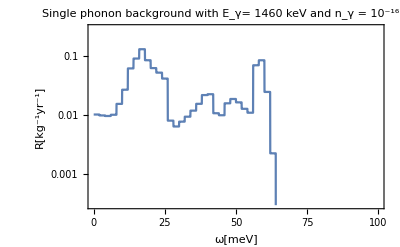

```mathematica
(*this should take less than a minute*)
RSi[ω_]=Rate1n[MNSi,NTSi,SiDOS,FqSi,{{1460,10^-16}} ];
LogPlot[{RSi[ω*10^-6]},{ω,0,140},Frame->True,PlotRange->{{0,100},{0.3*10^-3,0.3}},FrameLabel-> {"ω[meV]","R[kg^-1yr^-1]"},PlotLabel-> "Single phonon background with E_γ= 1460 keV and n_γ = 10^-16 cm^-3"]
```

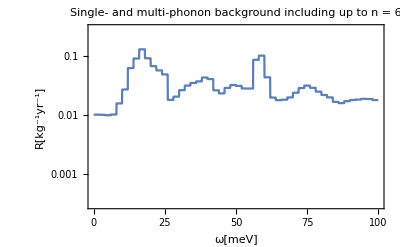

```mathematica
(*this will take ~10 minutes*)
RSi6[ω_]=Rate[MNSi,NTSi,SiDOS,FqSi,{{1460,10^-16}} ][[1]];
LogPlot[{RSi6[ω*10^-6]},{ω,0,140},PlotRange->{{0,100},{0.3*10^-3,0.3}},Frame->True,FrameLabel-> {"ω[meV]","R[kg^-1yr^-1]"},PlotLabel-> "Single- and multi-phonon background including up to n = 6"]
```